# Report Project 1

Course code: IX1501
Date: 2020-09-04

Magnus Fredriksson, magfred@kth.se
Fredrik Öberg, fobe@kth.se

Task 1: Winning a Teddy

## Summary

### Task

-Graphics-

At a dice game you throw five dice in the form of the Platonic solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up.

At a fun-fair you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy.

Determine the exact (no floating point, please) probability function of the sum.

Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

Determine the expected investment to win a Teddy.

What’s the probability of winning (at least one) Teddy if you play twenty times?

### Result

1) Determine the exact probability function of the sum.

The total probability function when combining the probability mass functions of each individual dice (P(S=s)) is derived from creating convolutions between each individual dice function

Pdfs(x)= Pdf4(x)*Pdf6(x)*Pdf8(x)*Pdf12(x)*Pdf20(x)

where the star indicates the convolution between each individual function. This gives us the probability function

Pdfs={0,0,0,0,1/46080,1/9216,1/3072,7/9216,23/15360,121/46080,97/23040,29/4608,409/46080,61/5120,707/46080,293/15360,53/2304,311/11520,95/3072,1597/46080,39/1024,379/9216,1007/23040,211/4608,1091/23040,223/4608,1127/23040,1127/23040,223/4608,1091/23040,211/4608,1007/23040,379/9216,39/1024,1597/46080,95/3072,311/11520,53/2304,293/15360,707/46080,61/5120,409/46080,29/4608,97/23040,121/46080,23/15360,7/9216,1/3072,1/9216,1/46080}

where the index of the list(beginning with 1) indicates the value of the given probability. Value 5 has a probability of 1/46080, 6 has a probability of 1/9216 and so forth. This is visualised in the following graph:

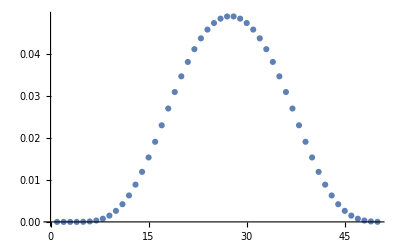

##### 2) Determine the exact probability of winning the Teddy prize. Also give a floating point answer.

To determine the exact probability of winning the Teddy, we can simply sum all the mutually exclusive outcomes that satisfies the win condition, sum of dice is less or equal to 10, or greater or equal to 40.

Since the distribution is symmetrical, we can multiply the chance of the sum being less or equal to 10 by 2 or. We can also get the result by subtracting the chance of getting the sum in the interval 11 to 44 from 1. This results in  (41/3840) , or 0.0107.

##### 3) Determine the expected investment to win a Teddy.

To determine the expected investment to win a teddy we first need to calculate the expected value E(X) of the function Pdfs. It is a geometric distribution function of the type

                  ∑_(i=1)^∞ i(1-p)^(i-1)P             
                  
which can be simplified  to 1/p by using the value of geometric series being equal to 1/(1-x) if -1 < x < 1. (see example 5.2 in the course book “Sannolikhetsteori och statistikteori med tillämpningar”). When P = 41/3840 the expected value becomes

E(X)= 1/(41/3840) = 3840/41 =  93.6585

By multiplying that number with the cost of each try (2 euros) we get the expected investment of winning a Teddy to 187.317 euros.

##### 4) What’s the probability of winning (at least one) Teddy if you play twenty times?

The probability of winning the first teddy on the n’th try is equal to the probability of losing n-1 times, then winning 1 time. With the probability of winning as P, This can be written as (1-P)^(n-1)P. To get the probability of winning in 20 or less tries, we can simply sum the probability of winning on tries 1...n.

                 ∑_(i=1)^n (1-p)^(i-1)P

We went with the way of calculating the probability through subtracting the probability of  not winning any teddy in 20 tries from 1. This simplifies it to 1-(1-P)^20, and comes out to 0.1932.

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
tetracube=ListConvolve[ConstantArray[1/4, 4], ConstantArray[1/6,6],{1,-1},0];
octadode=ListConvolve[ConstantArray[1/8, 8], ConstantArray[1/12,12],{1,-1},0];
tetracubeoctadode=ListConvolve[tetracube, octadode,{1,-1},0];
pdftot=ListConvolve[tetracubeoctadode, ConstantArray[1/20,20],{1,-1},0];
pdftotshift=Join[{0,0,0,0},pdftot]
```

{0,0,0,0,1/46080,1/9216,1/3072,7/9216,23/15360,121/46080,97/23040,29/4608,409/46080,61/5120,707/46080,293/15360,53/2304,311/11520,95/3072,1597/46080,39/1024,379/9216,1007/23040,211/4608,1091/23040,223/4608,1127/23040,1127/23040,223/4608,1091/23040,211/4608,1007/23040,379/9216,39/1024,1597/46080,95/3072,311/11520,53/2304,293/15360,707/46080,61/5120,409/46080,29/4608,97/23040,121/46080,23/15360,7/9216,1/3072,1/9216,1/46080}

```mathematica
ListPlot[pdftotshift]
```

-Graphics-

```mathematica
probtot=1-Total[pdftotshift[[11;;44]]]
probtot=Total[pdftotshift[[1;;10]]]*2
```

41/3840

41/3840

```mathematica
1/probtot
```

3840/41

```mathematica
N[1/probtot]
```

93.6585

```mathematica
N[1/probtot]*2
```

187.317

```mathematica
N[Sum[i(1-probtot)^(i-1)*probtot,{i,1,Infinity}]]
```

93.6585

```mathematica
N[1-(1-probtot)^20]
```

0.193208

```mathematica
N[Sum[(1-probtot)^(i-1)*probtot,{i,1,20}]]
```

0.193208